### KBragg = π, π, π (Andor2) KDiffuse = π { sin30, cos30 - cosθ, sinθ } (Andor1) θ is the angle that we use between the Bragg beam and lattice 2 retro.

```mathematica
KBragg={π,π,π};
θ=ArcTan[0.5/8.75];
KDiffuse={π/2,π((√3)/2-Cos[θ]),π Sin[θ]};
```

### Below, we define expressions for the crystal and spin structure factors in an infinite crystal, as a function of the Bragg scattering vector K. The K vector in units of the inverse lattice spacing is

```mathematica
Cfun[K_,Sites_]:=Sin[K[[1]] Sites/2.]^2/Sin[K[[1]]/2]^2 Sin[K[[2]] Sites/2.]^2/Sin[K[[2]]/2]^2 Sin[K[[3]] Sites/2.]^2/Sin[K[[3]]/2]^2
Sfun[K_,Sites_]:=Sin[(K[[1]] +π)Sites/2.]^2/Sin[(K[[1]]+π)/2]^2 Sin[(K[[2]] +π)Sites/2.]^2/Sin[(K[[2]]+π)/2]^2 Sin[(K[[3]] +π)Sites/2.]^2/Sin[(K[[3]]+π)/2]^2
```

```mathematica
Cfun[KBragg,10]
Cfun[KDiffuse,1000]
Sfun[KDiffuse,10.0000001]
```

5.2709×10^-92

1.00566×10^-23

0.98026

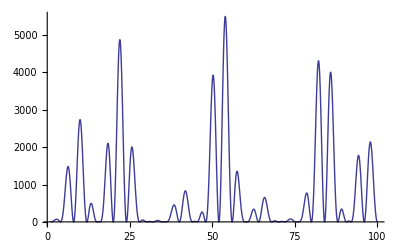

```mathematica
Plot[Cfun[KDiffuse,Sites],{Sites,1,100}]
```

### Below, we define expressions for the crystal and spin structure factors as a function of the Bragg scattering vector K. The K vector in units of the inverse lattice spacing is

```mathematica
CCSum[K_]:=Module[{Cminus,Sites=10},
Cminus=Total[Flatten[
Table[
Table[
Table[Exp[I (K[[1]] i+K[[2]] j+K[[3]] k)],
{i,1,Sites}],
{j,1,Sites}],
{k,1,Sites}]
]];
Abs[Cminus]^2
]

CC[K_,Sites_]:=Module[{Cminus,Cplus},

Cminus=Total[Flatten[
Table[
Table[
Table[Exp[I (K[[1]] i+K[[2]] j+K[[3]] k)],
{i,1,Sites}],
{j,1,Sites}],
{k,1,Sites}]
]];

Cplus=Total[Flatten[
Table[
Table[
Table[Exp[I (-K[[1]] i-K[[2]] j-K[[3]] k)],
{i,1,Sites}],
{j,1,Sites}],
{k,1,Sites}]
]];
Cminus Cplus
]

SSum[K_]:=Module[{Sminus,Sites=10},
Sminus=Total[Flatten[
Table[
Table[
Table[Exp[I (K[[1]] i+K[[2]] j+K[[3]] k)](Mod[i+j+k,2]-1./2),
{i,1,Sites}],
{j,1,Sites}],
{k,1,Sites}]
]];

Abs[Sminus]^2
]

S[K_,Sites_]:=Module[{Sminus,Splus},

Sminus=Total[Flatten[
Table[
Table[
Table[Exp[I (K[[1]] i+K[[2]] j+K[[3]] k)](Mod[i+j+k,2]-1./2),
{i,1,Sites}],
{j,1,Sites}],
{k,1,Sites}]
]];

Splus=Total[Flatten[
Table[
Table[
Table[Exp[I (-K[[1]] i-K[[2]] j-K[[3]] k)](Mod[i+j+k,2]-1/2.),
{i,1,Sites}],
{j,1,Sites}],
{k,1,Sites}]
]];
Sminus Splus
]
```

### Verify that the defined sums give reasonable values

```mathematica
CC[KBragg,10.]
CC[KDiffuse,10.]
S[KDiffuse,10.]
S[KBragg,10.]
```

0

2728.74+0. ⅈ

0.245065+0. ⅈ

250000.

```mathematica
CCSum[KBragg]
CCSum[KDiffuse]
SSum[KDiffuse]
SSum[KBragg]
```

0

2728.74

0.245065

250000.

```mathematica
FullSimplify[1/(2d/√(1+s)+I)1/(2d/√(1+s)-I)]
```

(1+s)/(1+4 d^2+s)

### Find the expression for the scattering cross section that depends on the laser beam detuning and the direction in which we are looking. Detuning is with respect to halfway between states 1 and 2. Spacing between 1 and 2 is 12.9 linewidths. Bragg should optimally be at 0.

```mathematica
sigma[det_,K_,s_]:=Module[{f1,f2,α,β},

f1=1/(2 (det-12.9/2)/√(1+s)+I);
f2=1/(2(det+12.9/2)/√(1+s)+I);

α=1/4(Abs[f1+f2])^2;
β=(Abs[f1-f2])^2;
(α CCSum[K]+β SSum[K])((1+det^2)/(1+det^2+s))+α(1-(1+det^2)/(1+det^2+s))
]
```

### Plot the cross sections

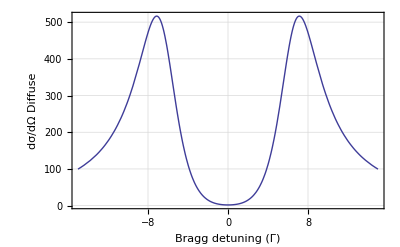

```mathematica
θ=ArcTan[0.5/8.75];
Plot[{sigma[det,KDiffuse,25]},{det,-15,15},
PlotRange->All,
GridLines->Automatic,
Frame->True,FrameLabel->{"Bragg detuning (Γ)","dσ/dΩ Diffuse"},
LabelStyle->Directive[FontFamily->"Times",FontSize->18,Bold],
ImageSize->{400}
]
```

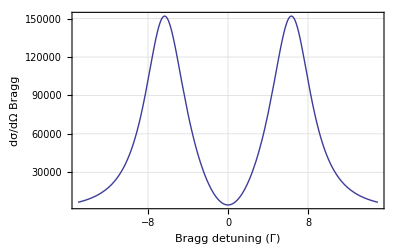

```mathematica
Plot[{sigma[det,KBragg,25]},{det,-15,15},
PlotRange->All,
GridLines->Automatic,
Frame->True,FrameLabel->{"Bragg detuning (Γ)","dσ/dΩ Bragg"},
LabelStyle->Directive[FontFamily->"Times",FontSize->18,Bold],
ImageSize->{400}
]
```

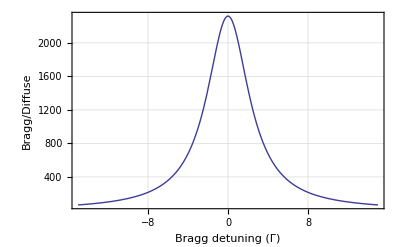

```mathematica
Plot[{sigma[det,KBragg,25]/sigma[det,KDiffuse,25]},{det,-15,15},
PlotRange->All,
GridLines->Automatic,
Frame->True,FrameLabel->{"Bragg detuning (Γ)","Bragg/Diffuse"},
LabelStyle->Directive[FontFamily->"Times",FontSize->18,Bold],
ImageSize->{400}
]
```

## Other stuff

{{2,30.3915+0. ⅈ},{5,408.869+0. ⅈ},{7,996.364+0. ⅈ},{10,2728.74+0. ⅈ},{11,1159.55+0. ⅈ},{12,4.26971×10^-27+0. ⅈ},{13,447.062+0. ⅈ},{14,277.93+0. ⅈ},{15,1.50612+0. ⅈ}}

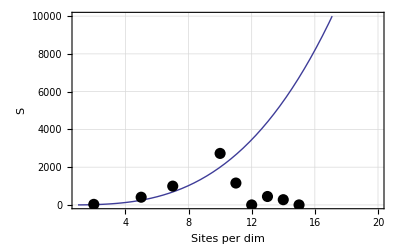

```mathematica
sitesTable=Table[{Sites,CC[KDiffuse,Sites]},{Sites,{2,5,7,10,11,12,13,14,15}}]
Plot[{2 t^3},{t,1,20},
PlotRange->{0.,10000},
GridLines->Automatic,
Frame->True,FrameLabel->{"Sites per dim","S"},
LabelStyle->Directive[FontFamily->"Times",FontSize->22,Bold],
ImageSize->{400},
Epilog->{PointSize[0.02],Map[Point,sitesTable]}
]
```

{{2,64.},{5,15625.},{7,117649.},{10,1.×10^6}}

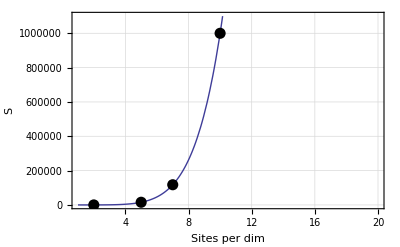

```mathematica
sitesTable=Table[{Sites,4 S[KBragg,Sites]},{Sites,{2,5,7,10}}]
Plot[{t^6},{t,1,20},
PlotRange->{0.,1100000},
GridLines->Automatic,
Frame->True,FrameLabel->{"Sites per dim","S"},
LabelStyle->Directive[FontFamily->"Times",FontSize->22,Bold],
ImageSize->{400},
Epilog->{PointSize[0.02],Map[Point,sitesTable]}
]
```

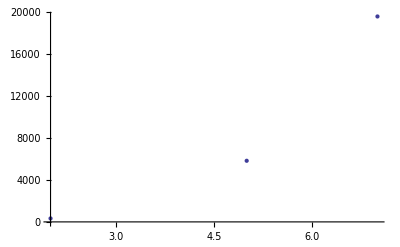

```mathematica
ListPlot[Table[{Sites,Bragg[Sites]},{Sites,{2,5,7}}]]
```

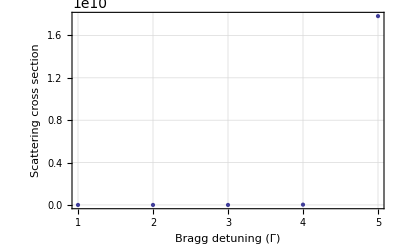

```mathematica
θ=ArcTan[0.5/8.75];

Plot[
Table[Bragg[Sites],{Sites,{2,5,10,25,45}}]
,
PlotRange->All,
GridLines->Automatic,
Frame->True,FrameLabel->{"Bragg detuning (Γ)","Scattering cross section"},
LabelStyle->Directive[FontFamily->"Times",FontSize->18,Bold],
ImageSize->{400}
]
```

```mathematica
CC[{π,π,π}]
```

0

```mathematica
S[{π,π,π}]
```

250000.

```mathematica
S[{-π,-π,-π}]
```

62500.

```mathematica
Total[Flatten[m[[1]]]]
```

50

```mathematica
"
```

```mathematica
m[[1,1,1]]
```

{0,1,0,1,0,1,0,1,0,1,0}

```mathematica
m[[1]]
```

{{{0,1,0,1,0,1,0,1,0,1,0},{1,0,1,0,1,0,1,0,1,0,1},{0,1,0,1,0,1,0,1,0,1,0},{1,0,1,0,1,0,1,0,1,0,1},{0,1,0,1,0,1,0,1,0,1,0},{1,0,1,0,1,0,1,0,1,0,1},{0,1,0,1,0,1,0,1,0,1,0},{1,0,1,0,1,0,1,0,1,0,1},{0,1,0,1,0,1,0,1,0,1,0},{1,0,1,0,1,0,1,0,1,0,1},{0,1,0,1,0,1,0,1,0,1,0}},{{1,0,1,0,1,0,1,0,1,0,1},{0,1,0,1,0,1,0,1,0,1,0},{1,0,1,0,1,0,1,0,1,0,1},{0,1,0,1,0,1,0,1,0,1,0},{1,0,1,0,1,0,1,0,1,0,1},{0,1,0,1,0,1,0,1,0,1,0},{1,0,1,0,1,0,1,0,1,0,1},{0,1,0,1,0,1,0,1,0,1,0},{1,0,1,0,1,0,1,0,1,0,1},{0,1,0,1,0,1,0,1,0,1,0},{1,0,1,0,1,0,1,0,1,0,1}},{{0,1,0,1,0,1,0,1,0,1,0},{1,0,1,0,1,0,1,0,1,0,1},{0,1,0,1,0,1,0,1,0,1,0},{1,0,1,0,1,0,1,0,1,0,1},{0,1,0,1,0,1,0,1,0,1,0},{1,0,1,0,1,0,1,0,1,0,1},{0,1,0,1,0,1,0,1,0,1,0},{1,0,1,0,1,0,1,0,1,0,1},{0,1,0,1,0,1,0,1,0,1,0},{1,0,1,0,1,0,1,0,1,0,1},{0,1,0,1,0,1,0,1,0,1,0}},{{1,0,1,0,1,0,1,0,1,0,1},{0,1,0,1,0,1,0,1,0,1,0},{1,0,1,0,1,0,1,0,1,0,1},{0,1,0,1,0,1,0,1,0,1,0},{1,0,1,0,1,0,1,0,1,0,1},{0,1,0,1,0,1,0,1,0,1,0},{1,0,1,0,1,0,1,0,1,0,1},{0,1,0,1,0,1,0,1,0,1,0},{1,0,1,0,1,0,1,0,1,0,1},{0,1,0,1,0,1,0,1,0,1,0},{1,0,1,0,1,0,1,0,1,0,1}},{{0,1,0,1,0,1,0,1,0,1,0},{1,0,1,0,1,0,1,0,1,0,1},{0,1,0,1,0,1,0,1,0,1,0},{1,0,1,0,1,0,1,0,1,0,1},{0,1,0,1,0,1,0,1,0,1,0},{1,0,1,0,1,0,1,0,1,0,1},{0,1,0,1,0,1,0,1,0,1,0},{1,0,1,0,1,0,1,0,1,0,1},{0,1,0,1,0,1,0,1,0,1,0},{1,0,1,0,1,0,1,0,1,0,1},{0,1,0,1,0,1,0,1,0,1,0}},{{1,0,1,0,1,0,1,0,1,0,1},{0,1,0,1,0,1,0,1,0,1,0},{1,0,1,0,1,0,1,0,1,0,1},{0,1,0,1,0,1,0,1,0,1,0},{1,0,1,0,1,0,1,0,1,0,1},{0,1,0,1,0,1,0,1,0,1,0},{1,0,1,0,1,0,1,0,1,0,1},{0,1,0,1,0,1,0,1,0,1,0},{1,0,1,0,1,0,1,0,1,0,1},{0,1,0,1,0,1,0,1,0,1,0},{1,0,1,0,1,0,1,0,1,0,1}},{{0,1,0,1,0,1,0,1,0,1,0},{1,0,1,0,1,0,1,0,1,0,1},{0,1,0,1,0,1,0,1,0,1,0},{1,0,1,0,1,0,1,0,1,0,1},{0,1,0,1,0,1,0,1,0,1,0},{1,0,1,0,1,0,1,0,1,0,1},{0,1,0,1,0,1,0,1,0,1,0},{1,0,1,0,1,0,1,0,1,0,1},{0,1,0,1,0,1,0,1,0,1,0},{1,0,1,0,1,0,1,0,1,0,1},{0,1,0,1,0,1,0,1,0,1,0}},{{1,0,1,0,1,0,1,0,1,0,1},{0,1,0,1,0,1,0,1,0,1,0},{1,0,1,0,1,0,1,0,1,0,1},{0,1,0,1,0,1,0,1,0,1,0},{1,0,1,0,1,0,1,0,1,0,1},{0,1,0,1,0,1,0,1,0,1,0},{1,0,1,0,1,0,1,0,1,0,1},{0,1,0,1,0,1,0,1,0,1,0},{1,0,1,0,1,0,1,0,1,0,1},{0,1,0,1,0,1,0,1,0,1,0},{1,0,1,0,1,0,1,0,1,0,1}},{{0,1,0,1,0,1,0,1,0,1,0},{1,0,1,0,1,0,1,0,1,0,1},{0,1,0,1,0,1,0,1,0,1,0},{1,0,1,0,1,0,1,0,1,0,1},{0,1,0,1,0,1,0,1,0,1,0},{1,0,1,0,1,0,1,0,1,0,1},{0,1,0,1,0,1,0,1,0,1,0},{1,0,1,0,1,0,1,0,1,0,1},{0,1,0,1,0,1,0,1,0,1,0},{1,0,1,0,1,0,1,0,1,0,1},{0,1,0,1,0,1,0,1,0,1,0}},{{1,0,1,0,1,0,1,0,1,0,1},{0,1,0,1,0,1,0,1,0,1,0},{1,0,1,0,1,0,1,0,1,0,1},{0,1,0,1,0,1,0,1,0,1,0},{1,0,1,0,1,0,1,0,1,0,1},{0,1,0,1,0,1,0,1,0,1,0},{1,0,1,0,1,0,1,0,1,0,1},{0,1,0,1,0,1,0,1,0,1,0},{1,0,1,0,1,0,1,0,1,0,1},{0,1,0,1,0,1,0,1,0,1,0},{1,0,1,0,1,0,1,0,1,0,1}},{{0,1,0,1,0,1,0,1,0,1,0},{1,0,1,0,1,0,1,0,1,0,1},{0,1,0,1,0,1,0,1,0,1,0},{1,0,1,0,1,0,1,0,1,0,1},{0,1,0,1,0,1,0,1,0,1,0},{1,0,1,0,1,0,1,0,1,0,1},{0,1,0,1,0,1,0,1,0,1,0},{1,0,1,0,1,0,1,0,1,0,1},{0,1,0,1,0,1,0,1,0,1,0},{1,0,1,0,1,0,1,0,1,0,1},{0,1,0,1,0,1,0,1,0,1,0}}}